# A necessary stabilization condition for PID control - Naiam Bajcinca - 2005

## Julián Hernández - 18/Abr/22

```mathematica
(*-Graphics-
El generador de frecuencias singulares des de la forma:
-Graphics-
tomando en cuenta que es la parte imaginaria de P(jω).*)
```

```mathematica
(*-Graphics-*)
```

```mathematica
A[s_]:=-1/2 s^4-7 s^3-2s+1
B[s_]:=s^7+11 s^6+46 s^5+95 s^4+109 s^3+74 s^2+24s
Co[s_,kp_,ki_,kd_]:=ki+kp*s+kd*s^2
P[s_,kp_,ki_,kd_]:=A[s]*Co[s,kp,ki,kd]+B[s]
Ra=FullSimplify[ComplexExpand[Re[A[I*ω]]]];
Ia=FullSimplify[ComplexExpand[Im[A[I*ω]]]];
Rb=FullSimplify[ComplexExpand[Re[B[I*ω]]]];
Ib=FullSimplify[ComplexExpand[Im[B[I*ω]]]];
```

```mathematica
NSolve[A[s]==0,s]
```

{{s→-14.0211},{s→-0.163643-0.618621 ⅈ},{s→-0.163643+0.618621 ⅈ},{s→0.348358}}

```mathematica
sω=ω/.Solve[-2*ω==-(Ra*Ib-Ia*Rb)/(Ra^2+Ia^2),ω,Reals];
sω1=sω[[6;;9]];
sω2=AppendTo[sω1,0];
N[sω2]
```

{0.352973,0.663758,0.774175,3.34727,0.}

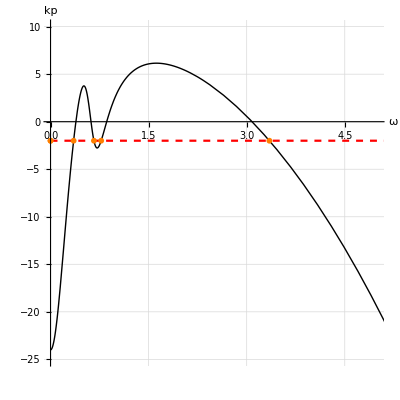

```mathematica
kpω=FullSimplify[-(Ra*Ib-Ia*Rb)/(Ra^2+Ia^2)*1/ω];
f1=ParametricPlot[{ω,kpω},{ω,0,10},PlotRange->{{0,5},{-25,10}},GridLines->Automatic,AspectRatio->1,AxesLabel->{ω,kp},Frame->False,PlotStyle->{Black,Thick}];
f2=ParametricPlot[{ω,-2},{ω,0,10},PlotStyle->{Red,Dashed}];
f3=ListPlot[{{0,-2},{sω2[[5]],-2},{sω2[[1]],-2},{sω2[[2]],-2},{sω2[[3]],-2},{sω2[[4]],-2}},PlotStyle->{Orange}, PlotMarkers->{Automatic,AbsolutePointSize[6]}];
Show[f1,f2,f3]
```

```mathematica
FindMaximum[kpω,{ω,0,5}]
```

{3.76642,{ω→0.510005}}

```mathematica
FindMaxValue[kpω,ω]
```

6.15651

```mathematica
FindMinValue[kpω,ω]
```

-2.76135

```mathematica
FindMinimum[kpω,{ω,0.8,1}]
```

{-2.76135,{ω→0.712879}}

```mathematica
FindMinimum[kpω,{ω,0,5}]
```

{-24.,{ω→-1.06079×10^-9}}

```mathematica
(*De acuerdo al Teorema 3, se tiene N=7, M=4, y P=1. El Teorema 5 afirma que para al estabilidad debe existir un kp tal que Z≥1/2 E/(N-M+2P)=2 raices. Observando el gráfico anterior se puede observar que la condición que se debe cumplir es -24<kp<6.15. De hecho,el lector puede comprobar que existen controladores PID estables dentro de este intervalo de kp.*)
```

```mathematica
(*Tomando como ejemplo kp=-2, se debe obtener ki=5, kd=10*)
```

```mathematica
Solve[ComplexExpand[Re[P[ω*I,-2,ki,kd]]]==0,kd]
```

{{kd→(-2 ki+156 ω^2-218 ω^4+ki ω^4+22 ω^6)/(ω^2 (-2+ω^4))}}

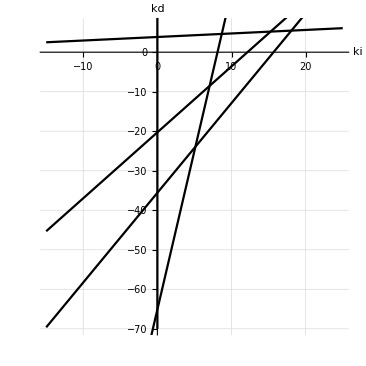

```mathematica
kdω[ω_,ki_]:=(-2 ki+156 ω^2-218 ω^4+ki ω^4+22 ω^6)/(ω^2 (-2+ω^4));
f4=ParametricPlot[{ki,kdω[0.3529,ki]},{ki,-15,25},PlotRange->{{-15,25},{-70,7}},GridLines->Automatic,AspectRatio->1,PlotStyle->{Black},AxesLabel->{ki,kd}];
f5=ParametricPlot[{ki,kdω[0.6637,ki]},{ki,-15,25},PlotStyle->{Black}];
f6=ParametricPlot[{ki,kdω[0.7741,ki]},{ki,-15,25},PlotStyle->{Black}];
f7=ParametricPlot[{ki,kdω[3.3472,ki]},{ki,-15,25},PlotStyle->{Black}];
f8=ParametricPlot[{0,kd},{kd,-70,20},PlotStyle->{Black}];
Show[f4,f5,f6,f7,f8]
```

```mathematica
Table[ki-(sω2[[k]])^2*kd+((Ra*Rb+Ia*Ib)/(Ra^2+Ia^2)/.ω->sω2[[k]])==0,{k,1,5}]
```

{ki-kd (Root0.353Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2+((1-1/2 (Root0.353Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^4) (-74 (Root0.353Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2+95 (Root0.353Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^4-11 (Root0.353Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^6)-(Root0.353Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2 (-2+7 (Root0.353Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2) (-24+109 (Root0.353Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2-46 (Root0.353Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^4+(Root0.353Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^6))/((Root0.353Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2 (-2+7 (Root0.353Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2)^2+(1-1/2 (Root0.353Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^4)^2)==0,ki-kd (Root0.664Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2+((1-1/2 (Root0.664Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^4) (-74 (Root0.664Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2+95 (Root0.664Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^4-11 (Root0.664Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^6)-(Root0.664Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2 (-2+7 (Root0.664Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2) (-24+109 (Root0.664Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2-46 (Root0.664Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^4+(Root0.664Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^6))/((Root0.664Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2 (-2+7 (Root0.664Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2)^2+(1-1/2 (Root0.664Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^4)^2)==0,ki-kd (Root0.774Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2+((1-1/2 (Root0.774Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^4) (-74 (Root0.774Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2+95 (Root0.774Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^4-11 (Root0.774Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^6)-(Root0.774Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2 (-2+7 (Root0.774Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2) (-24+109 (Root0.774Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2-46 (Root0.774Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^4+(Root0.774Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^6))/((Root0.774Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2 (-2+7 (Root0.774Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2)^2+(1-1/2 (Root0.774Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^4)^2)==0,ki-kd (Root3.35Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2+((1-1/2 (Root3.35Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^4) (-74 (Root3.35Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2+95 (Root3.35Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^4-11 (Root3.35Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^6)-(Root3.35Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2 (-2+7 (Root3.35Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2) (-24+109 (Root3.35Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2-46 (Root3.35Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^4+(Root3.35Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^6))/((Root3.35Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2 (-2+7 (Root3.35Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2)^2+(1-1/2 (Root3.35Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^4)^2)==0,ki==0}

```mathematica
N[Table[ki-(sω2[[k]])^2*kd+((Ra*Rb+Ia*Ib)/(Ra^2+Ia^2)/.ω->sω2[[k]])==0,{k,1,5}]]
```

{-8.11027-0.12459 kd+ki==0.,-15.6687-0.440575 kd+ki==0.,-12.1438-0.599346 kd+ki==0.,43.1031-11.2042 kd+ki==0.,ki==0.}

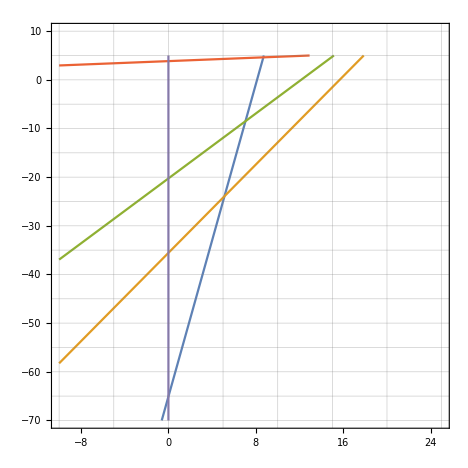

```mathematica
ContourPlot[{ki-kd (Root"0.353"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2+((1-1/2 (Root"0.353"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^4) (-74 (Root"0.353"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2+95 (Root"0.353"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^4-11 (Root"0.353"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^6)-(Root"0.353"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2 (-2+7 (Root"0.353"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2) (-24+109 (Root"0.353"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2-46 (Root"0.353"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^4+(Root"0.353"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^6))/((Root"0.353"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2 (-2+7 (Root"0.353"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^2)^2+(1-1/2 (Root"0.353"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,5]0.3529729727394526)^4)^2)==0,ki-kd (Root"0.664"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2+((1-1/2 (Root"0.664"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^4) (-74 (Root"0.664"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2+95 (Root"0.664"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^4-11 (Root"0.664"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^6)-(Root"0.664"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2 (-2+7 (Root"0.664"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2) (-24+109 (Root"0.664"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2-46 (Root"0.664"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^4+(Root"0.664"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^6))/((Root"0.664"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2 (-2+7 (Root"0.664"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^2)^2+(1-1/2 (Root"0.664"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,6]0.6637578660000256)^4)^2)==0,ki-kd (Root"0.774"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2+((1-1/2 (Root"0.774"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^4) (-74 (Root"0.774"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2+95 (Root"0.774"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^4-11 (Root"0.774"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^6)-(Root"0.774"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2 (-2+7 (Root"0.774"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2) (-24+109 (Root"0.774"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2-46 (Root"0.774"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^4+(Root"0.774"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^6))/((Root"0.774"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2 (-2+7 (Root"0.774"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^2)^2+(1-1/2 (Root"0.774"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,7]0.7741745302039708)^4)^2)==0,ki-kd (Root"3.35"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2+((1-1/2 (Root"3.35"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^4) (-74 (Root"3.35"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2+95 (Root"3.35"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^4-11 (Root"3.35"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^6)-(Root"3.35"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2 (-2+7 (Root"3.35"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2) (-24+109 (Root"3.35"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2-46 (Root"3.35"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^4+(Root"3.35"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^6))/((Root"3.35"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2 (-2+7 (Root"3.35"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^2)^2+(1-1/2 (Root"3.35"Root[44-530 #1^2+1600 #1^4-1463 #1^6+107 #1^8+#1^10&,8]3.347272107531678)^4)^2)==0,ki==0},{ki,-10,25},{kd,-70,5},PlotRange->{{-10,25},{-70,10}},GridLines->{Table[i,{i,-10,25,5}],Table[j,{j,-70,20,5}]}]
```